```mathematica
2
```

2

# PHSX 591 Solar Flares & CMEs

## Problem Set 1 Roy Smart Due Feb. 15th

```mathematica
Clear["Global`*"]
```

## Problem 1

### Part a.

#### The flux function for Figure 1a is given by

```mathematica
Ap = λ ArcTan[(y+b)/z]-λ ArcTan[(y+a)/z]+λ ArcTan[(y-a)/z]-λ ArcTan[(y-b)/z];
```

#### Define the assumptions for this expression

```mathematica
$Assumptions = λ >0 && a > 0  && z>0 && b > a  && c >0 && Ics< 0
```

λ>0&&a>0&&z>0&&b>a&&c>0&&Ics<0

#### Plot this function to see what it looks like

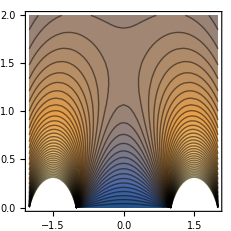

```mathematica
ContourPlot[Ap /. {b-> 2, a-> 1, λ->1},{y,-2,2},{z,0,2},Contours->50]
```

#### The X point is located where the magnetic field is equal to zero. Therefore, we will begin by taking a derivative of the flux function to determine the magnetic field.

```mathematica
Bp = Cross[Grad[Ap,{x,y,z}],{1,0,0}] //FullSimplify
```

{0,((a (1/(1+(a-y)^2/z^2)+1/(1+(a+y)^2/z^2))+y (-1/(1+(a-y)^2/z^2)+1/(1+(b-y)^2/z^2)+1/(1+(a+y)^2/z^2)-1/(1+(b+y)^2/z^2))-b/(1+(b-y)^2/z^2)-b/(1+(b+y)^2/z^2)) λ)/z^2,((-1/(1+(a-y)^2/z^2)+1/(1+(b-y)^2/z^2)+1/(1+(a+y)^2/z^2)-1/(1+(b+y)^2/z^2)) λ)/z}

#### Evaluate this field at y=0

```mathematica
Bpz = Bp /. y -> 0
```

{0,(((2 a)/(1+a^2/z^2)-(2 b)/(1+b^2/z^2)) λ)/z^2,0}

#### Find the height for which all components of the magnetic field are zero by solving the y-component for z

```mathematica
sol1aa=Solve[Bpz[[2]] == 0, z] //FullSimplify
```

{{z→-√(a b)},{z→√(a b)}}

#### Select the positive solution, since we are interested in the height of the X point above the photosphere

```mathematica
zx = sol1aa[[2,1,2]]
```

√(a b)

#### The flux between this X point and the origin is given by evaluating the flux function at this X point.

```mathematica
ψp12 = Ap /. {y-> 0,z-> zx} //FullSimplify
```

2 λ (-ArcTan[√(a/b)]+ArcTan[√(b/a)])

#### Check limit by expanding about a/b=0

```mathematica
Series[ψp12 /. b-> 1,{a,0,1}]/. a -> 0
```

π λ

#### Check another limit by expanding about a/b=1

```mathematica
Series[ψp12 /. b-> 1,{a,1,1}] /.a-> 1 //Quiet
```

0

### Part b.

#### The change in flux can be written as

```mathematica
Δψp12 = (ψp12 /. a -> a+ Δa ) - ψp12 //FullSimplify
```

2 λ (ArcTan[√(a/b)]-ArcTan[√(b/a)]+ArcTan[√(b/(a+Δa))]-ArcTan[√((a+Δa)/b)])

#### Expand the change in flux about Δa/a=0 to leading order.

```mathematica
Δψp12/.b-> 2a/. a-> 1
```

2 λ (ArcTan[1/(√2)]-ArcTan[√2]+ArcTan[√2 √(1/(1+Δa))]-ArcTan[(√(1+Δa))/(√2)])

```mathematica
Δψp12=Normal[Series[Δψp12/.b-> 2a/. a-> 1,{Δa,0,1}]] /. Δa -> Δa/a
```

-(2 √2 Δa λ)/(3 a)

### Part c.

#### The potential field after the wire is added is given by

```mathematica
A = Ap + Ics/c Log[(y^2 + (z+h)^2)/(y^2+(z-h)^2)]
```

λ ArcTan[(-a+y)/z]-λ ArcTan[(a+y)/z]-λ ArcTan[(-b+y)/z]+λ ArcTan[(b+y)/z]+(Ics Log[(y^2+(h+z)^2)/(y^2+(-h+z)^2)])/c

```mathematica
ContourPlot[A /. {b-> 2, a-> 1, λ->1, Ics->-0.01, c-> 1,h->√2},{y,-2,2},{z,0,3},Contours->150]
```

-Graphics-

#### Again, the null points are where the magnetic field is equal to zero. Start by calculating the new magnetic field for this new potential

```mathematica
B = Cross[Grad[A,{x,y,z}],{1,0,0}] //FullSimplify
```

{0,(4 h Ics (h^2+y^2-z^2))/(c (y^2+(h-z)^2) (y^2+(h+z)^2))+((a-y)/((a-y)^2+z^2)+(-b+y)/((b-y)^2+z^2)+(a+y)/((a+y)^2+z^2)-(b+y)/((b+y)^2+z^2)) λ,(8 h Ics y z)/(c (y^2+(h-z)^2) (y^2+(h+z)^2))+z (-1/((a-y)^2+z^2)+1/((b-y)^2+z^2)+1/((a+y)^2+z^2)-1/((b+y)^2+z^2)) λ}

#### Evaluate this field at y=0, since we know the nulls are located on the z-axis

```mathematica
By = (B /. y-> 0 )[[2]] // FullSimplify
```

(4 h Ics)/(c h^2-c z^2)+(2 a λ)/(a^2+z^2)-(2 b λ)/(b^2+z^2)

#### Now solve for the exact height of the nulls. We will define a quantity Ir^2=Ics/cλ to use for expanding expressions.

```mathematica
h=zx;
sol2=Solve[By  == 0,z] ;
zn1=sol2[[2,1,2]] /.Ics -> c λ Ir^2//Simplify
zn2 = sol2[[4,1,2]]/.Ics -> c λ Ir^2 //Simplify
```

√((a^2 b-a b^2+√(a^5 b) Ir^2+√(a b^5) Ir^2-(a+b) √(a (a-b) b Ir^2 (2 √(a b)+a Ir^2-b Ir^2)))/(a-b-2 √(a b) Ir^2))

√((a^2 b-a b^2+√(a^5 b) Ir^2+√(a b^5) Ir^2+(a+b) √(a (a-b) b Ir^2 (2 √(a b)+a Ir^2-b Ir^2)))/(a-b-2 √(a b) Ir^2))

#### Expand the exact expression for the location of the nulls for small current

```mathematica
zna1 = Series[zn1, {Ir,0,1}] //Normal //Simplify
zna2 = Series[zn2, {Ir,0,1}]//Normal  //Simplify
```

1/2 √(a b) (2-(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4)))

1/2 √(a b) (2+(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4)))

#### Write answer in terms of current

```mathematica
(z1 =zna1 /. Ir -> √(Ics/(c λ))//Simplify)//Framed
(z2 =zna2 /. Ir -> √(Ics/(c λ))//Simplify)//Framed
```

1/2 √(a b) (2-(√2 (a+b) √(Ics/(a c λ-b c λ)))/(a b)^(1/4))

1/2 √(a b) (2+(√2 (a+b) √(Ics/(a c λ-b c λ)))/(a b)^(1/4))

#### Check our answer by evaluating the flux function for both nulls and verifying that they are the same. Start by evaluating the exact expression for the flux function at the nulls.

```mathematica
A1 =A /. Ics-> c λ Ir^2/. y-> 0/. z -> zna1  //Simplify
A2=A /. Ics-> c λ Ir^2/. y-> 0/.z -> zna2 // Simplify
```

λ (-2 ArcTan[(2 a)/(√(a b) (2-(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+2 ArcTan[(2 b)/(√(a b) (2-(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+Ir^2 Log[((-4 √(a-b) (a b)^(1/4)+√2 a Ir+√2 b Ir)^2)/(2 (a+b)^2 Ir^2)])

λ (-2 ArcTan[(2 a)/(√(a b) (2+(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+2 ArcTan[(2 b)/(√(a b) (2+(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+Ir^2 Log[((4 √(a-b) (a b)^(1/4)+√2 a Ir+√2 b Ir)^2)/(2 (a+b)^2 Ir^2)])

#### next, expand the argument of the logarithm for small current.

```mathematica
A1[[2,3,2,1]]=Series[A1[[2,3,2,1]],{Ir,0,-2}] // Normal;
A2[[2,3,2,1]]=Series[A2[[2,3,2,1]],{Ir,0,-2}] // Normal;
A1
A2
```

λ (-2 ArcTan[(2 a)/(√(a b) (2-(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+2 ArcTan[(2 b)/(√(a b) (2-(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+Ir^2 Log[(8 (a-b) √(a b))/((a+b)^2 Ir^2)])

λ (-2 ArcTan[(2 a)/(√(a b) (2+(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+2 ArcTan[(2 b)/(√(a b) (2+(√2 (a+b) Ir)/(√(a-b) (a b)^(1/4))))]+Ir^2 Log[(8 (a-b) √(a b))/((a+b)^2 Ir^2)])

#### Finally, expand the rest of the expression for small current

```mathematica
(ψ12 =Series[A1,{Ir,0,2}] //Simplify //Normal)//Framed
(Series[A2,{Ir,0,2}] //Simplify // Normal)// Framed
```

2 λ (-ArcTan[√(a/b)]+ArcTan[√(b/a)])+Ir^2 λ (1+Log[(8 (a-b) √(a b))/(a+b)^2]-2 Log[Ir])

2 λ (-ArcTan[√(a/b)]+ArcTan[√(b/a)])+Ir^2 λ (1+Log[(8 (a-b) √(a b))/(a+b)^2]-2 Log[Ir])

#### the flux function for both nulls is the same value to leading order.

### Part d.

#### Compute the flux difference

```mathematica
Δψ12a = ψ12 - ψp12 /.Ir -> √(Ics/(c λ))/. b-> 2a  //Expand
```

Ics/c+(Ics Log[-(8 √2 √(a^2))/(9 a)])/c-(2 Ics Log[√(Ics/(c λ))])/c

#### The logarithm terms provide the largest contribution to the flux since the current is small.

```mathematica
(Δψ12b = Δψ12a[[2]] + Δψ12a[[3]] //Simplify) //Framed
```

-(Ics Log[-(9 Ics)/(8 √2 c λ)])/c

#### Find the length of the current sheet by finding the distance between the nulls

```mathematica
(L = 1/2(z2-z1) /. b-> 2a //Simplify) //Framed
```

(3 a)/(2^(1/4) √(-(c λ)/Ics))

### Part e.

#### Perform a variable substitution to write given integral in terms of current

```mathematica
dΔψ12 = D[Δψ12b, Ics]
```

-1/c-Log[-(9 Ics)/(8 √2 c λ)]/c

#### Perform the integral to find the change in energy

```mathematica
(ΔϵM = 1/c∫Ics dΔψ12 ⅆIcs //Simplify)//Framed
```

-(Ics^2 (1+2 Log[-(9 Ics)/(8 √2 c λ)]))/(4 c^2)

### Part f.

#### Ampere’s law is given as

```mathematica
amp = -(4 π Ics)/c==4 L Bi;
```

#### Solve for the magnetic field

```mathematica
Clear[Bi]
sol2 = Solve[amp, Bi];
(Bi = sol2[[1,1,2]] //FullSimplify) //Framed
```

(2^(1/4) π λ)/(3 a √(-(c λ)/Ics))

#### Now, the Alven speed is

```mathematica
vA = Bi/(√(μ0 ρ0)) //FullSimplify;
```

#### We can use this to find the Alven transit time, given as

```mathematica
(τA = (2L)/vA //FullSimplify) //Framed
```

(9 √2 a^2 √(μ0 ρ0))/(π λ)

### Part g.

#### Save the provided values to memory

```mathematica
values={a->3 10^9 Quantity[, "Centimeters"],b -> 6 10^9 Quantity[, "Centimeters"],Lx ->10^10 Quantity[, "Centimeters"],ψSrc -> 10^22 Quantity[, "Maxwells"],Δa -> -10^9 Quantity[, "Centimeters"],c -> 3 10^10 Quantity[, ("Centimeters")/("Seconds")],μ0 ->  4 π 10^-7 Quantity[, ("Henries")/("Meters")]};
```

#### Find the value of the parameter λ evaluating the flux function at y=∞

```mathematica
(λV = N[ψSrc/(π Lx)/. values]) //Framed
```

3.1831×10^11 Mx/cm

```mathematica
AppendTo[values, λ-> λV];
```

#### Solve for the current by equating the change in flux from part b. to that found in part d.

```mathematica
Icgs2mks = 10^8/((10 Quantity[, ("Henries")/("Meters")])(3 10^10 Quantity[, ("Centimeters")/("Seconds")]));
sol3=NSolve[Δψp12 == Δψ12b /. values, Ics];
IcsV = Re[sol3[[1,1,2]]];
AppendTo[values,Ics -> IcsV];
UnitConvert[IcsV Icgs2mks,"amps"] //Framed
```

-4.90637×10^12 A

#### Now we are free to find a value for the length of the current sheet using the results of part d.

```mathematica
L /. values //Framed
```

9.39594×10^9 cm

#### The height of the current sheet was found in part c.

```mathematica
N[h /. values] //Framed
```

4.24264×10^9 cm

#### and the energy was found in part e.

```mathematica
(ΔϵMV = UnitConvert[ΔϵM Lx / μ0/. values,"ergs"]) //Framed
```

-6.74193×10^31 ergs

### Part h.

#### Save the additional numeric values to memory

```mathematica
vribV = vrib -> 3 Quantity[, ("Kilometers")/("Seconds")];
Bz0V = Bz0 -> 300 Quantity[, "Gauss"];
```

```mathematica
AppendTo[values, vribV];
AppendTo[values, Bz0V];
```

#### The total reconnection time can be found by equating the change in flux to the product of the magnetic field and the change in area. We then solve the expression for time. Note: the factor of 2 is due to the two flare ribbons.

```mathematica
(τrx = UnitConvert[Δψ12b/(2 Bz0 vrib) /. values, "seconds"]) //Framed
```

555.751 s

#### we are then free to compute the average power using the quotient of the total energy release and the total reconnection time

```mathematica
(PM = ΔϵMV / τrx) //Framed
```

-1.21312×10^29 ergs/s

#### The electric field is the negative change in flux per unit length

```mathematica
(EM = UnitConvert[- Δψ12b / τrx /. values, "volts/meter"]) //Framed
```

-180. V/m

#### The energy flux incident on each ribbon is

```mathematica
PM/(2Lx vrib τrx) /. values // Framed
```

-3.63808×10^10 ergs/(cm^2 s)

```mathematica
AppendTo[values,ρ0 ->  10^-15 Quantity[, ("Grams")/("Centimeters")^3]];
machnum = UnitConvert[τA /. values,"second"] / τrx //Framed
```

0.023106

```mathematica
τA /. values
```

0.000406074 √g cm √H/Mx

```mathematica
UnitConvert[τA /. values,"second"]
```

12.8412 s